```mathematica
1/(4/3-1)
```

3

```mathematica
1/(5/3-1)
```

3/2

```mathematica
(7/12)
```

```mathematica
(4/12)
```

1/3

```mathematica
Prad=(4/12)*Urad0
Ppair=(7/12)*Urad0*exp
Upair=Ppair/(4/3-1)
```

Urad0/3

(7 exp Urad0)/12

(7 exp Urad0)/4

```mathematica
(4/3-1)
```

1/3

```mathematica
(5/3-1)
```

2/3

```mathematica
(1/12)/(Pi^2/15)
```

5/(4 π^2)

```mathematica
arad
```

arad

```mathematica
hbar=h/(2*Pi)
arad1=8*Pi^5*kb^4/(15*h^3*c^3)
arad2=Pi^2*kb^4/(15*(hbar*c)^3)
FullSimplify[arad1-arad2]
```

h/(2 π)

(8 kb^4 π^5)/(15 c^3 h^3)

(8 kb^4 π^5)/(15 c^3 h^3)

0

```mathematica
one=(15*4/7)^(1/2)/12
```

(√(5/21))/2

```mathematica
two=Sqrt[5/84]
FullSimplify[one-two]
```

(√(5/21))/2

0

```mathematica
15*4
```

60

```mathematica
E1=((me*c^2)^2+2*hbar*c*q*b)^(1/2)-me*c^2
```

-c^2 me+√(c^4 me^2+(b c h q)/π)

```mathematica
Series[E1,{b,0,1}]
```

(-c^2 me+√(c^4 me^2))+(h √(c^4 me^2) q b)/(2 c^3 me^2 π)+O[b]^2

```mathematica
gam=1/Sqrt[1-beta^2]
FullSimplify[gam*(1+beta^2*gam^2),beta≥0]
FullSimplify[gam*(1+beta^2*gam^2)//.{beta->Sqrt[1-1/gamm^2]},gamm≥1]
```

1/(√(1-beta^2))

1/((1-beta^2)^(3/2))

gamm^3

```mathematica
FullSimplify[gam^3-gam*(1+beta^2*gam^2)]
```

0

```mathematica
Series[gam^3,{beta,0,4}]
```

1+(3 beta^2)/2+O[beta]^4

```mathematica
Series[gam,{beta,0,4}]
```

1+beta^2/2+(3 beta^4)/8+O[beta]^5

```mathematica
Series[gam*(1+beta^2*gam^2),{beta,0,4}]
```

1+(3 beta^2)/2+(15 beta^4)/8+O[beta]^5

```mathematica
gam^3//.{beta->0.1}
gam*(1+beta^2*gam^2)//.{beta->0.1}
```

1.01519

1.01519

```mathematica
(* mu=me c^2 / (kb T_e) *)
```

```mathematica
omegap=Sqrt[MeijerG[{{0},{2}},{{-1/2,1,3/2},{0}},mu^2/4]/(2*BesselK[2,mu])]
```

(√(MeijerG[{{},{2}},{{-1/2,1,3/2},{}},mu^2/4]/BesselK[2,mu]))/(√2)

```mathematica
FullSimplify[Normal[Series[omegap,{mu,Infinity,1}]],{mu>0}]
```

1-5/(4 mu)

```mathematica
top=FullSimplify[Normal[Series[MeijerG[{{0},{2}},{{-1/2,1,3/2},{0}},mu^2/4],{mu,Infinity,2}]],{mu>0}]
bottom=FullSimplify[Normal[Series[(2*BesselK[2,mu]),{mu,Infinity,2}]],{mu>0}]
omegapfactorlargemu=Sqrt[top/bottom]
```

(ⅇ^-mu (-5+8 mu) √(π/2))/(4 mu^(3/2))

(ⅇ^-mu (15+8 mu) √(π/2))/(4 mu^(3/2))

√((-5+8 mu)/(15+8 mu))

```mathematica
omegaplargemu//.{mu->100}
```

√(159/163)

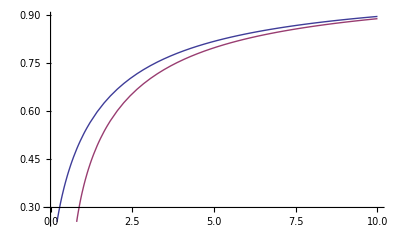

```mathematica
Plot[{omegap,omegaplargemu},{mu,0,10}]
```

```mathematica
Clear[omegaprelfactor]
```

```mathematica
omega
```

```mathematica
omegaprelfactor[1.0]
```

0.526498

```mathematica
solsT
```

{T→1000000000}

```mathematica
omegap//.{mu->10.}
```

```mathematica
omegap//.{mu->100}
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$Aborted

```mathematica
(8*Pi/3)*(q^2/(me*c^2))^2
```

6.65077×10^-25

```mathematica
delta=1/(gamma*(1-beta*Cos[h]))
intit=Integrate[delta^4*Sin[h],{h,0,Pi}]
fsintit=FullSimplify[intit,{beta≥0,gamma≥1,beta<1,Re[ArcSec[beta]]==0}]
```

1/(gamma (1-beta Cos[h]))

1/gamma^4 If[(beta∉Reals||-1≤Re[beta]≤1)&&(ArcCsc[beta]∉Reals||Re[ArcSec[beta]]≤0||Re[ArcSec[beta]]≥π)&&beta≠-1&&beta≠1,-(2 (3+beta^2))/(3 (-1+beta^2)^3),Integrate[Sin[h]/(-1+beta Cos[h])^4,{h,0,π},Assumptions→!((beta∉Reals||-1≤Re[beta]≤1)&&(ArcCos[1/beta]∉Reals||Re[ArcCos[1/beta]]≤0||Re[ArcCos[1/beta]]≥π)&&beta≠-1&&beta≠1)]]

-(2 (3+beta^2))/(3 (-1+beta^2)^3 gamma^4)

```mathematica
(fsintit*Lp*(1/2))//.{beta->Sqrt[1-1/gamma^2]}
```

1/3 (4-1/gamma^2) gamma^2 Lp

```mathematica
1/3 (4-1/gamma^2) //.{gamma->1/Sqrt[1-b^2]}
```

1/3 (3+b^2)

```mathematica
3800/50.
```

76.